# Twin Engine Propeller Driven Airplane

```mathematica
ClearAll[Evaluate[Context[]<>"*"]]
```

## Weight Estimation

### Mission Specification

```mathematica
AirCraftType="Single Engine Propeller";
MS=Import["D:\\Aerospace\\Aerospace-2023\\3_Third Year\\Second Semester\\AER 3910_Aircraft design and manufacture [125 marks]\\PreMidtermCode(TwinEngine)\\ExcelTables\\TwinMissionSpecs.csv","Dataset","HeaderLines"->{1,1}]
```

### Mission Profile

### Solution Procedure

#### From Table 2.15, for twin engine propeller driven

```mathematica
AB=Import["D:\\Aerospace\\Aerospace-2023\\3_Third Year\\Second Semester\\AER 3910_Aircraft design and manufacture [125 marks]\\WTO-A,B.csv","Dataset","HeaderLines"->1];
WR=Import["D:\\Aerospace\\Aerospace-2023\\3_Third Year\\Second Semester\\AER 3910_Aircraft design and manufacture [125 marks]\\Weight fractions.csv","Dataset","HeaderLines"->{1,1}]
```

```mathematica
aE=AB[4,"A"]; Print["A = ",aE]
bE=AB[4,"B"]; Print["B = ",bE]
```

A = -0.144

B = 1.1162

#### Mission fuel fraction

```mathematica
WRP={};(*Weight Ration of each phase*)
```

Phase 1 : Engine Start and Warm - up 
Phase 2 : Taxi 
Phase 3 : Take - off 
Phase 4 : Climb 
(as indicated in Table 2.1)

```mathematica
WRP=Catenate[{WRP,WR[2,#]&/@{1,2,3,4}}];
```

If the Climb was inclined

```mathematica
Vcl=275.;(*average climb speed (kts->nmph)— assumed if not given*)
rcl=2500.;(*average climb-rate (fpm)*)
Alt=20000
Ecl=Alt/rcl;(*endurance of climb (min)*)
Rcl=Ecl/60.×Vcl;(*range of climb (nm)*)
```

20000

Phase 5 : Cruise (using Breguet’ s range equation)

```mathematica
ηp=0.8;
cp=0.5;
LpD=10;
Rcr=MS[6,1];
Rcr=Rcr-Rcl; (*Uncomment if the climb was inclined*)sol=Solve[Rcr==375 ηp/cp×LpD×Log[WRP5^-1],WRP5];
WRP=Append[WRP,WRP5/.sol[[1]]];
np=0.7
cpp=0.6
Ld=11
Vltr=120
Eltr=0.5
sol1=Solve[Eltr==375*(1/Vltr)np/cpp×Ld×Log[WRP6^-1],WRP6];
WRP=Append[WRP,WRP6/.sol1[[1]]];
```

0.7

0.6

11

120

0.5

Phase 6 : Descent 
Phase 7 : Landing, Taxi, Shutdown
(as indicated in Table 2.1)

```mathematica
WRP=Catenate[{WRP,WR[2,#]&/@{7,8}}];
TableForm[{WRP},TableHeadings->{{"Weight Ratios"},{"W_1/W_TO","W_2/W_1","W_3/W_2","W_4/W_3","W_5/W_4","W_6/W_5","W_7/W_6"}}]
```

| W_1/W_TO | W_2/W_1 | W_3/W_2 | W_4/W_3 | W_5/W_4 | W_6/W_5 | W_7/W_6 | 
Weight Ratios | 0.995 | 0.997 | 0.998 | 0.992 | 0.925684 | 0.98761 | 0.993 | 0.993

```mathematica
Mff=∏_(i=1)^MS[1,1] WRP[[i]];
```

#### C and D calculation

```mathematica
cE=1.-(1.+MS[7,1])×(1.-Mff)-MS[8,1]; Print["C = ",cE]
dE=MS[5,1]; Print["D = ",dE]
```

C = 0.851668

D = 1600

#### Take - off Weight

```mathematica
eqn=Wto-(10.^((Log[Wto]/Log[10.]-aE)/bE)+dE)/cE;
WTO = Wto/.FindRoot[Simplify[eqn]==0,{Wto,7000}];
```

#### Empty Weight

```mathematica
WE=cE×WTO-dE;
```

#### Fuel Weight

```mathematica
Wf=(1+MS[7,1])×(1-Mff)×WTO;
```

### Preliminary numbers for the given mission specifications

```mathematica
Print["M_ff = ",Mff]
Print["W_TO = ",WTO," lbs"]
Print["W_E = ",WE," lbs"]
Print["W_f = ",Wf," lbs"]
```

M_ff = 0.885334

W_TO = 5320.84 lbs

W_E = 2931.59 lbs

W_f = 762.649 lbs

## Take-off Weight Sensitivity

```mathematica
Sen = {};
```

#### Airplane growth factor due to payload

```mathematica
Sen=Append[Sen,bE*WTO(dE-cE(1-bE)WTO)^-1];
```

#### Airplane growth factor due to empty weight

```mathematica
Sen=Append[Sen,bE*WTO(10.^((Log[10,WTO]-aE)/bE))^-1];
```

The factor F is defined as
F= - B W_TO^2{CW_TO(1-B)D}^-1(1+M_res)M_ff

```mathematica
Mres = MS[7,1];
F = - bE×WTO^2(cE×WTO(1-bE)-dE)^-1(1+Mres)Mff
```

16445.2

#### Airplane growth factor due to range

Using formula for propeller driven in range case where y = R stated in table 2.20

```mathematica
Sen=Append[Sen,F×cp×(375.×ηp×LpD)^-1];
```

#### Airplane growth factor due to endurance and velocity

Not applicable as mentioned in [2]

```mathematica
Sen=Catenate[{Sen,{"-","-"}}];
```

#### Airplane growth factor due to specific fuel consumption

Using formula for propeller driven in range case where y = C_p stated in table 2.20

```mathematica
Sen=Append[Sen,F×Rcr×(375.×ηp×LpD)^-1];
F×Rcr×(375.×ηp×LpD)^-1
```

2539.87

#### Airplane growth factor due to propeller efficiency

Using formula for propeller driven in range case where y = η_p stated in table 2.20

```mathematica
Sen=Append[Sen,-F×Rcr×cp×(375.×ηp^2×LpD)^-1];
-F×Rcr×cp×(375.×ηp^2×LpD)^-1
Rcr×cp×(375.×ηp^2×LpD)^-1
```

-1587.42

0.0965278

#### Airplane growth factor due to lift-to-drag ration

Using formula for propeller driven in range case where y = L/D stated in table 2.20

```mathematica
Sen=Append[Sen,-F×Rcr×cp×(375.×ηp×LpD^2)^-1];
```

#### Results

```mathematica
TableForm[{Sen[[#]]}&/@{1,2,3,4,5,6,7,8},TableHeadings->{{"(∂SubscriptBox[W, TO])/(∂SubscriptBox[W, pl])","(∂SubscriptBox[W, TO])/(∂SubscriptBox[W, E])","(∂SubscriptBox[W, TO])/(∂R)","(∂SubscriptBox[W, TO])/(∂E)","(∂SubscriptBox[W, TO])/(∂V)","(∂SubscriptBox[W, TO])/(∂SubscriptBox[C, p])","(∂SubscriptBox[W, TO])/(∂SubscriptBox[η, p])","(∂SubscriptBox[W, TO])/(∂L/D)"}}]
```

(∂SubscriptBox[W, TO])/(∂SubscriptBox[W, pl]) | 2.79282
(∂SubscriptBox[W, TO])/(∂SubscriptBox[W, E]) | 2.02591
(∂SubscriptBox[W, TO])/(∂R) | 2.74087
(∂SubscriptBox[W, TO])/(∂E) | -
(∂SubscriptBox[W, TO])/(∂V) | -
(∂SubscriptBox[W, TO])/(∂SubscriptBox[C, p]) | 2539.87
(∂SubscriptBox[W, TO])/(∂SubscriptBox[η, p]) | -1587.42
(∂SubscriptBox[W, TO])/(∂L/D) | -126.994

#### The variation in the design gross weight due to the mentioned changes

```mathematica
dWTO[ΔWpl_,ΔWE_,ΔR_,ΔE_,ΔV_,ΔCp_,Δηp_,ΔLpD_]:= ΔWpl×Sen[[1]]+ΔWE×Sen[[2]]+ΔR×Sen[[3]]+ΔE×Sen[[4]]+ΔV×Sen[[5]]+ΔCp×Sen[[6]]+Δηp×Sen[[7]]+ΔLpD×Sen[[8]]
dWTO[0,0,0,0,0,-0.1,0.1,0]
```

-412.73

## Matching Plot

```mathematica
ρ=MS[14,1];
ρU=Quantity[ρ,"SlugsMass"/("Feet")^3];
```

### Sizing to Take-off Distance Requirements

According to FAR 23

Sketch the curve of the equation (W/S) (W/P) at various C_Lmax

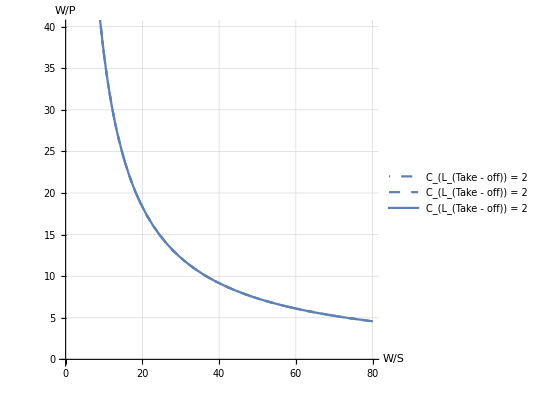

Take-off Parameter = 183.232
 W/P = 366.463/(W/S)

```mathematica
STOG = MS[12,1];
(*solTO=Solve[STO==8.14 top + 0.0149 top^2&&top>0,top];*)
solTO=Solve[STOG==4.9 top + 0.009 top^2&&top>0,top];
TOP=top/.solTO[[1]];
σTO=1.; (*The density at altitude to std sealevel denisty ratio*)
CLt = {2,2,2};
ps={DotDashed,Dashed,Bold};
WpPTO[CLMaxt_,WpSTO_] := (CLMaxt×TOP×σTO)/WpSTO
Print["Sketch the curve of the equation (W/S) (W/P) at various C_Lmax"]
Tplot = Show[ParametricPlot[{WpS, WpPTO[CLt[[#]],WpS]},{WpS,0,80},GridLines->Automatic,AspectRatio->1,AxesLabel->{"W/S","W/P"},PlotLegends->{StringForm["C_(L_(Take - off)) = ``",CLt[[#]]]},PlotStyle->ps[[#]],PlotRange->{{0,80},{0,40}}]&/@{1,2,3}]
Print["Take-off Parameter = ",TOP,"\n W/P = " ,WpPTO[CLt[[1]],"W/S"]]
```

### Sizing to Landing Distance Requirements

According to FAR 25

98.3608

Sketch the critical landing wing loading fraction at various C_Lmax

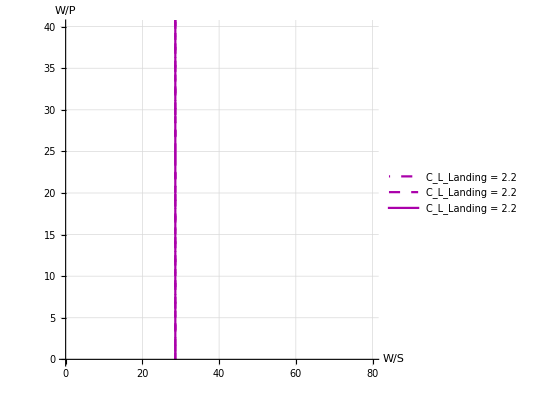

Stall Speed at Landing = 98.3608 ft/s
W_L/S = 25.3074
W_TO/S = 28.5852

```mathematica
SLG = MS[13,1];
(*Vsl=√(SL/0.5136)×1.68781; (*Converted from kts to fps*)*)
Vsl=√(SLG/0.265)×1.68781 (*Converted from kts to fps*)
LpT = Mff; (*Subscript[W, L]/Subscript[W, TO]=0.95 = Subscript[M, ff]*)
CLl={2.2,2.2,2.2}; (*Arbitrary Subscript[C, Subscript[Lmax, TO]] values in the range from Table 3.1 for Twin Propeller A/C*)
ps={DotDashed,Dashed,Bold};
WpSL[CLMaxl_] := (1/2×0.002378×Vsl^2)/LpT CLMaxl
Print["Sketch the critical landing wing loading fraction at various C_Lmax"]
Lplot = Show[ParametricPlot[{WpSL[CLl[[#]]],y},{y,0,80},GridLines->Automatic,AspectRatio->1,AxesLabel->{"W/S","W/P"},PlotLegends->{StringForm["C_L_Landing = ``",CLl[[#]]]},PlotStyle->{ps[[#]],Darker[Magenta]},PlotRange->{{0,80},{0,40}}]&/@{1,2,3}]
Print["Stall Speed at Landing = ",Quantity[Vsl,"fps"],"\nW_L/S = " ,LpT×WpSL[2.2],"\nW_TO/S = " ,WpSL[2.2]]
```

### Sizing to Climb Requirements

According to FAR 23.(65,67,77)

-Graphics-

#### Common Expressions

```mathematica
CL32CDmax[CDo_,ar_,o_]:=(1.345(ar×o)^(3/4))/CDo^(1/4)  (*Subscript[(Subscript[C, L]^(3/2)/Subscript[C, D]), max] as a function of the Subscript[C, D0], Aspect Ratio, and Oswald's Factor, respectively*)
CD[CDo_,CL_,ar_,i_,j_]:=(CDo+ΔCD0[[i]]+ΔCD0[[j]])+CL^2/(π×e[[i]]×ar)  (*Subscript[C, D] as a function of Subscript[C, D0], Subscript[C, L], Aspect Ration, Oswald's Factor, and two indices for Subscript[C, D] conributions, respectively*)
RCP[RC_]:= RC/33000                       (*Rate of Climb Parameter as function of Rate of Climb*)
CGRP[CGR_,LD_,CL_]:=(CGR + LD^-1)/(√CL)         (*Climb Gradient Parameter as a function of Climb Gradient, L/D, and Subscript[C, L], respectively*)
WpPRC[RCP_,WpS_,CL32CD_,ηp_,σ_]:=ηp/(RCP + (√WpS)/(19×CL32CD×√σ))
WpPCGR[CGRP_,WpS_,ηp_,σ_]:=(18.97×ηp×√σ)/(CGRP √WpS)
ΔCL = 0.2;                             (*Subscript[C, Subscript[L, Climb]] to Subscript[C, Subscript[L, maxTO]] safe margin*)
```

#### Drag Polar Preparation

```mathematica
cf = 0.005;                                            (*skin friction coefficient*)
AR = {8,10}; 
ΔCD0 = {0,0.015,0.06,0.02,0.005};                      (*clean, take-off flaps, landing flaps, landing gear, stopped propeller*)
e = {0.8,0.8,0.7,0.8};                                 (*clean, take-off flaps, landing flaps, landing gear*)
f[Cf_]:= Switch[Cf,0.009,{-2.0458,1.},0.008,{-2.0969,1.},0.007,{-2.1549,1.},0.006,{-2.2218,1.},0.005,{-2.301,1.},0.004,{-2.3979,1.},0.003,{-2.5229,1.},0.002,{-2.699,1.}]
a = f[cf][[1]];
b = f[cf][[2]];
g[AirplaneType_]:= Switch[AirplaneType,1,{1.2362,0.4319},2,{1.0892,0.5147},3,{0.8635,0.5632},4,{1.0447,0.5326},5,{0.2263,0.6977},6,{-0.0866,0.8099},7,{0.0199,0.7531},8,{0.8565,0.5423},9,{-0.1289,0.7506},10,{0.1628,0.7316},11,{0.6295,0.6708},12,{-1.1868,0.9609}]
c = g[3][[1]];
d = g[3][[2]];
solSW = Solve[Log[10,Swet]==c+d×Log[10,WTO],Swet];
SWet = Swet/.solSW[[1]];
solf = Solve[Log[10,fa]==a+b×Log[10,SWet],fa];
f = fa/.solf[[1]];


WpSavg = 35;                                           (*Subscript[(W/S), avg] in psf*)
S = WTO/WpSavg;                                           (*Wing planform area in ft^2*)
CD0 = f/S;                                              (*Parasite drag coefficient Subscript[C, D0]*)
Print["a = ",a,"\nb = ",b,"\nc = ",c,"\nd = ",d]
Print[" Wetted Area (S_Wet) = ",Quantity[SWet,("Feet")^2],"\n Equivalent Parasite Area(f) = ",Quantity[f,("Feet")^2],"\n Wing Planform Area(S) = ",Quantity[S,("Feet")^2],"\n Parasite Drag Coefficient (C_D0) = ",CD0]
```

a = -2.301
b = 1.
c = 0.8635
d = 0.5632

Wetted Area (S_Wet) = 916.162 ft^2
 Equivalent Parasite Area(f) = 4.58112 ft^2
 Wing Planform Area(S) = 152.024 ft^2
 Parasite Drag Coefficient (C_D0) = 0.0301342

#### FAR 23.65 (AEO)

Rate of Climb

Rate of Climb Parameter (RCP) = 0.00909091
Updated Parasite Drag Coefficient (C_D0)= 0.0451342
For AR = {8,10}, (C_L^(3/2)/C_D)_max = {11.7417,13.8808}

W/P = 0.8/(1/110+(0.0526316 √(W/S))/((C_L^(3/2)/C_D)_max))

(W/S)_TO 
 (pfs) | (W/P)_(max .  cont .)  
 (lbs/hp) | (W/P)_(max .  take - off)  
 (lbs/hp)
20 | 27.4565 | 24.9604
30 | 23.7796 | 21.6178
40 | 21.3673 | 19.4248
50 | 19.6143 | 17.8312

Sketch the Plot Matching the Climb Rate Requirements for FAR 23.65 at various AR

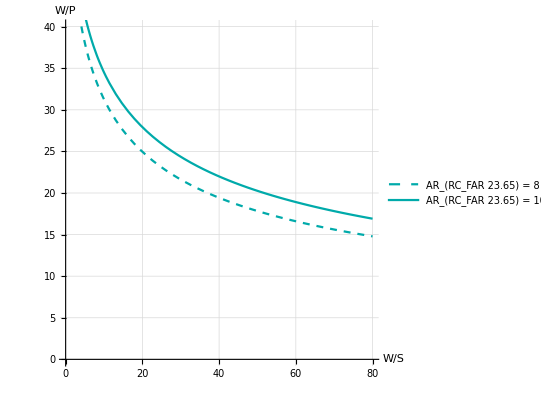

```mathematica
RC65 = 300;                                            (*Minimum rate of climb (fpm) according to FAR23.65*)
ηp65 = 0.8;                                            (*Assumed propeller efficiency*)
σ65 = 1.;                                              (*Density ratio according to FAR23.65*)
RCP65 = RCP[RC65];                                     (*Rate of climb parameter*)

CD065 = CD0 + ΔCD0[[2]];                                (* Parasite drag coefficient Subscript[C, D0] with take-off flaps*)
CL32CDmax65 = CL32CDmax[CD065,AR,e[[2]]];               (*Subscript[(Subscript[C, L]^(3/2)/Subscript[C, D]), max] for FAR 23.65*)
WpPRC65[WpSRC65_,CL32CD_]:= WpPRC[RCP65,WpSRC65,CL32CD,ηp65,σ65] 
Print["Rate of Climb Parameter (RCP) = ",RCP65//N,"\nUpdated Parasite Drag Coefficient (C_D0)= ",CD065,"\nFor AR = {8,10}, (C_L^(3/2)/C_D)_max = ",CL32CDmax65]
Print["W/P = ",WpPRC65["W/S","(C_L^(3/2)/C_D)_max"]]
TableForm[{#,WpPRC65[#,CL32CDmax65[[1]]],WpPRC65[#,CL32CDmax65[[1]]]/1.1}&/@{20,30,40,50},TableHeadings->{None,{"(W/S)_TO \n (pfs)","(W/P)_(max .  cont .)  \n (lbs/hp)","(W/P)_(max .  take - off)  \n (lbs/hp)"}}]

Print["Sketch the Plot Matching the Climb Rate Requirements for FAR 23.65 at various AR"]
RC65plot = Show[ParametricPlot[{WpS,WpPRC65[WpS,CL32CDmax65[[#]]]/1.1},{WpS,0,80},GridLines->Automatic,AspectRatio->1,AxesLabel->{"W/S","W/P"},PlotLegends->{StringForm["AR_(RC_FAR 23.65) = ``",AR[[#]]]},PlotStyle->{ps[[#+1]],Darker[Cyan]},PlotRange->{{0,80},{0,40}}]&/@{1,2}]
```

Climb Gradient

Climb Gradient Parameter (CGRP) = 0.151093
Drag Coefficient (C_D) = 0.172458
Lift Coeeficient (C_L_Climb) = 1.6
L/D = 9.27761

W/P = 100.441/(√(W/S))

(W/S)_TO 
 (pfs) | (W/P)_(max .  cont .)  
 (lbs/hp) | (W/P)_(max .  take - off)  
 (lbs/hp)
20 | 22.4593 | 19.0904
30 | 18.338 | 15.5873
40 | 15.8811 | 13.499
50 | 14.2045 | 12.0739

Sketch the Plot Matching the Climb Gradient Requirements for FAR 23.65

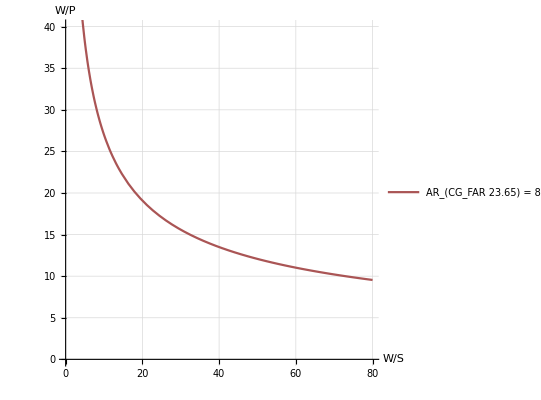

```mathematica
CGR65 = 1/12;                         (*Climb gradient in rad*)
CLmaxTOfd = 1.8;                      (*Subscript[C, Lmax]  with Take-off flaps down*)
CLmaxCGR65 = CLmaxTOfd - ΔCL;         (*Subscript[C, Subscript[L, Climb]]*)
CD65=CD[CD0,CLmaxCGR65,AR[[1]],2,1];
LpD65 = CLmaxCGR65/CD65;              (*L/D*)
CGRP65 = CGRP[CGR65,LpD65,CLmaxCGR65];
WpPCGR65[WpS65_]:= WpPCGR[CGRP65,WpS65,ηp65,σ65]
Print["Climb Gradient Parameter (CGRP) = ",CGRP65//N,"\nDrag Coefficient (C_D) = ",CD65,"\nLift Coeeficient (C_L_Climb) = ",CLmaxCGR65,"\nL/D = ",LpD65]
Print["W/P = ",WpPCGR65["W/S"]]
TableForm[{#,WpPCGR65[#],0.85×WpPCGR65[#]}&/@{20,30,40,50},TableHeadings->{None,{"(W/S)_TO \n (pfs)","(W/P)_(max .  cont .)  \n (lbs/hp)","(W/P)_(max .  take - off)  \n (lbs/hp)"}}]

Print["Sketch the Plot Matching the Climb Gradient Requirements for FAR 23.65"]
CGR65plot = Show[ParametricPlot[{WpS,0.85×WpPCGR65[WpS]},{WpS,0,80},GridLines->Automatic,AspectRatio->1,AxesLabel->{"W/S","W/P"},PlotLegends->{StringForm["AR_(CG_FAR 23.65) = ``",AR[[1]]]},PlotStyle->{ps[[#+2]],Darker[Pink]},PlotRange->{{0,80},{0,40}}]&/@{1}]
```

#### FAR 23.67 (OEI)

(W/S)_TO(pfs) | V_S_o(fps) | V_s_o(kts) | RC(fpm) | RCP(hp/lbs)
20 | 107.16 | 63.4908 | 108.839 | 0.00329816
30 | 131.244 | 77.7601 | 163.259 | 0.00494724
40 | 151.548 | 89.7896 | 217.679 | 0.00659632
50 | 169.436 | 100.388 | 272.098 | 0.0082454

Rate of Climb Parameter (RCP) = 0.000164908 W/S
Updated Parasite Drag Coefficient (C_D0)= 0.0351342
For AR = {8,10}, (C_L^(3/2)/C_D)_max = {12.5004,14.7777}

W/P = 0.8/((0.0566998 √(W/S))/((C_L^(3/2)/C_D)_max)+0.000164908 W/S)

(W/S)_TO 
(pfs) | (W/P)_(take - off) 
 for one engine 
 at 5,000 ft (lbs/hp) | (W/P)_(take - off) 
 for two engine 
 at 5,000 ft (lbs/hp) | (W/P)_(take - off) 
 for two engine 
 sealevel (lbs/hp)
20 | 33.9227 | 16.9614 | 14.4172
30 | 26.8537 | 13.4269 | 11.4128
40 | 22.6735 | 11.3368 | 9.63625
50 | 19.842 | 9.92099 | 8.43284

Sketch the Plot Matching the Rate of Climb Requirements for FAR 23.67 at various AR

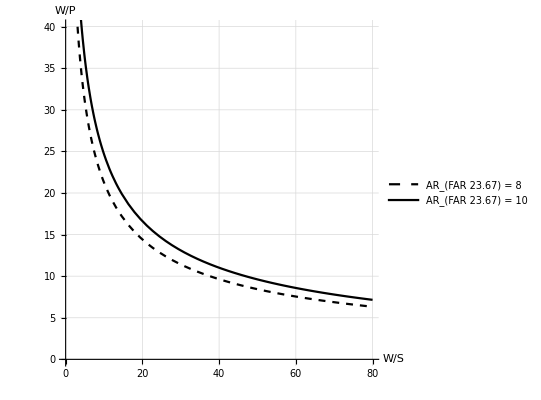

```mathematica
ρ5kft = 0.002049;                        (*The density of the atmosphere at 5,000 ft*)
 σ67 = ρ5kft/ρ;                           (*The density ratio at 5,000 ft*)
 ηp67 = 0.8;                              (*Propeller efficiency*)
 CLmaxClean = 1.7;                        (*Subscript[C, Lmax] at flaps-up configuration as the most favorable case*)
 Vso[WpS67_]:=1/1.68781 √((2 WpS67)/(ρ5kft×CLmaxClean)) (*Converted from fps to kts*)
 RC67[Vs_]:= 0.027×Vs^2
 RCP67[RC67_]:=RCP[RC67];
 TableForm[{{#},{1.68781×Vso[#]},{Vso[#]},{RC67[Vso[#]]},{RCP67[RC67[Vso[#]]]}}&/@{20,30,40,50},TableHeadings->{None,{"(W/S)_TO(pfs)","V_S_o(fps)","V_s_o(kts)","RC(fpm)","RCP(hp/lbs)"}}]
 
 CD067 = CD0 + ΔCD0[[5]];                                (* Parasite drag coefficient Subscript[C, D0] with gears up and flaps up (most favorable)*)
 CL32CDmax67 = CL32CDmax[CD067,AR,e[[1]]];               (*Subscript[(Subscript[C, L]^(3/2)/Subscript[C, D]), max] for FAR 23.67*)
 Print["Rate of Climb Parameter (RCP) = ",RCP67[RC67[Vso["W/S"]]],"\nUpdated Parasite Drag Coefficient (C_D0)= ",CD067,"\nFor AR = {8,10}, (C_L^(3/2)/C_D)_max = ",CL32CDmax67]
 WpPRC67[WpSRC67_,CL32CD_]:= WpPRC[RCP67[RC67[Vso[WpSRC67]]],WpSRC67,CL32CD,ηp67,σ67] 
 Print["W/P = ",WpPRC67["W/S","(C_L^(3/2)/C_D)_max"]]
 TableForm[{#,WpPRC67[#,CL32CDmax67[[1]]],WpPRC67[#,CL32CDmax67[[1]]]/2,(0.85/2)WpPRC67[#,CL32CDmax67[[1]]]}&/@{20,30,40,50},TableHeadings->{None,{"(W/S)_TO \n(pfs)","(W/P)_(take - off) \n for one engine \n at 5,000 ft (lbs/hp)","(W/P)_(take - off) \n for two engine \n at 5,000 ft (lbs/hp)","(W/P)_(take - off) \n for two engine \n sealevel (lbs/hp)"}}]

 
 Print["Sketch the Plot Matching the Rate of Climb Requirements for FAR 23.67 at various AR"]
 RC67plot = Show[ParametricPlot[{WpS,WpPRC67[WpS,CL32CDmax67[[#]]](0.85/2)},{WpS,0,80},GridLines->Automatic,AspectRatio->1,AxesLabel->{"W/S","W/P"},PlotLegends->{StringForm["AR_(FAR 23.67) = ``",AR[[#]]]},PlotStyle->{ps[[#+1]],Black},PlotRange->{{0,80},{0,40}}]&/@{1,2}]
```

#### FAR 23.77

Climb Gradient Parameter (CGRP) = 0.146711
Drag Coefficient (C_D) = 0.294299
Lift Coeeficient (C_L_Climb) = 1.8
L/D = 6.11622

W/P = 103.442/(√(W/S))

(W/S)_TO 
 (pfs) | (W/P)_(take - off)  
 (lbs/hp)
20 | 23.1303
30 | 18.8858
40 | 16.3556
50 | 14.6289

Sketch the Plot Matching the Climb Gradient Requirements for FAR 23.77

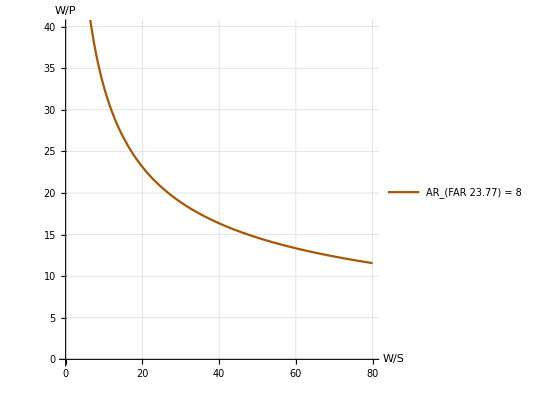

```mathematica
CGR77 = 1/30;                        (*Climb gradient in rad*)
ηp77 = 0.8;                          (*Assumed propeller efficiency*)
σ77 = 1.;                            (*Density ratio according to FAR23.77*)
CLmaxLfd = 2.;                       (*Subscript[C, Lmax]  with landing flaps down*)
CLmaxCGR77 = CLmaxLfd - ΔCL;         (*Subscript[C, Subscript[L, Climb]]*)
CD77=CD[CD0,CLmaxCGR77,AR[[1]],3,4];
LpD77 = CLmaxCGR77/CD77;
CGRP77 = CGRP[CGR77,LpD77,CLmaxCGR77];
Print["Climb Gradient Parameter (CGRP) = ",CGRP77//N,"\nDrag Coefficient (C_D) = ",CD77,"\nLift Coeeficient (C_L_Climb) = ",CLmaxCGR77,"\nL/D = ",LpD77]
WpPCGR77[WpS77_]:= WpPCGR[CGRP77,WpS77,ηp77,σ77]
Print["W/P = ",WpPCGR77["W/S"]]
TableForm[{#,WpPCGR77[#]}&/@{20,30,40,50},TableHeadings->{None,{"(W/S)_TO \n (pfs)","(W/P)_(take - off)  \n (lbs/hp)"}}]

Print["Sketch the Plot Matching the Climb Gradient Requirements for FAR 23.77"]
CGR77plot = Show[ParametricPlot[{WpS,WpPCGR77[WpS]},{WpS,0,80},GridLines->Automatic,AspectRatio->1,AxesLabel->{"W/S","W/P"},PlotLegends->{StringForm["AR_(FAR 23.77) = ``",AR[[1]]]},PlotStyle->{ps[[#+2]],Darker[Orange]},PlotRange->{{0,80},{0,40}}]&/@{1}]
```

### Sizing for Time-To-Climb and Ceiling Requirements

#### Time-to-Climb

For shallow flight path angles: γ < 15°

Rate of Climb at sealevel (RC_0) = 4023.59 ft/min
Rate of Climb at 10,000 ft (RC_h) = 804.719 ft/min
Rate of Climb Parameter (RCP) = 0.0243854
Parasite Drag Coeeficient (C_D_0) = 0.0301342
For AR = {8,10}, (C_L^(3/2)/C_D)_max = {12.9895,15.3559}

W/P = 0.8/(0.0243854+(0.0526316 √(W/S))/((C_L^(3/2)/C_D)_max))

(W/S)_TO 
 (pfs) | (W/P)_(take - off)  
 (lbs/hp)
20 | 18.8209
30 | 17.1754
40 | 15.9963
50 | 15.084

Sketch the Plot Matching the Time to Climb Requirements at various AR

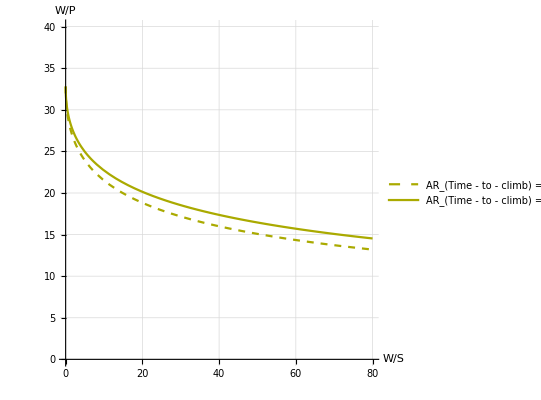

```mathematica
tcl = MS[11,1];                                                     (*time-to-climb in minutes*)
h = MS[9,1];
ηpTC = 0.8;
σTC = 1.;                                                            (*The Density ratio at the attitude for the design range*)
habs = 25000.;                                                       (*Absolute Ceiling from Table 3.7*)

RC0 = -habs/tcl Log[1-h/habs];                                             (*Rate of climb at sealevel in fpm*)
RCh = RC0(1-h/habs);

RCPTC = RCP[RCh];                                                     (*Rate of climb parameter*)

CD0TC = CD0 + ΔCD0[[1]];                                                (*Parasite drag coefficient Subscript[C, D0] in clean configuration*)
CL32CDmaxTC = CL32CDmax[CD0TC,AR,e[[1]]];                               (*Subscript[(Subscript[C, L]^(3/2)/Subscript[C, D]), max] for FAR 23.77*)

Print["Rate of Climb at sealevel (RC_0) = ",Quantity[RC0,"fpm"],"\nRate of Climb at 10,000 ft (RC_h) = ",Quantity[RCh,"fpm"],"\nRate of Climb Parameter (RCP) = ",RCPTC,"\nParasite Drag Coeeficient (C_D_0) = ",CD0TC,"\nFor AR = {8,10}, (C_L^(3/2)/C_D)_max = ",CL32CDmaxTC]
WpPRCTC[WpSRCTC_,CL32CD_]:= WpPRC[RCPTC,WpSRCTC,CL32CD,ηpTC,σTC] 
Print["W/P = ",WpPRCTC["W/S","(C_L^(3/2)/C_D)_max"]]
TableForm[{#,WpPRCTC[#,CL32CDmaxTC[[1]]]}&/@{20,30,40,50},TableHeadings->{None,{"(W/S)_TO \n (pfs)","(W/P)_(take - off)  \n (lbs/hp)"}}]

Print["Sketch the Plot Matching the Time to Climb Requirements at various AR"]
RCTCplot = Show[ParametricPlot[{WpS,WpPRCTC[WpS,CL32CDmaxTC[[#]]]},{WpS,0,80},GridLines->Automatic,AspectRatio->1,AxesLabel->{"W/S","W/P"},PlotLegends->{StringForm["AR_(Time - to - climb) = ``",AR[[#]]]},PlotStyle->{ps[[#+1]],Darker[Yellow]},PlotRange->{{0,80},{0,40}}]&/@{1,2}]
```

#### Ceiling Requirements

### Sizing for Cruise Speed Requirements

345.234

W/P = 0.234566 W/S

Sketch the Plot Matching the Cruise Speed Requirements at various Cruise Speeds

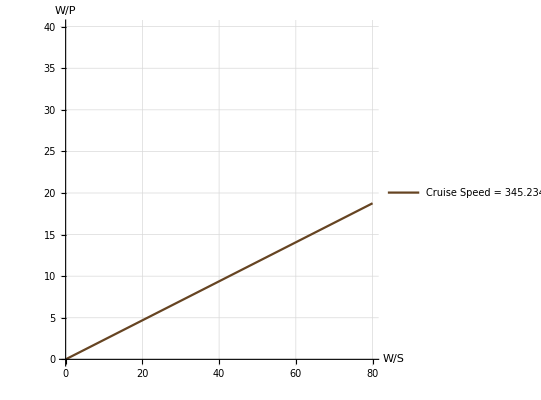

```mathematica
Vcr = 300.×1.15077945          (*average cruise speed (kts->nmph)— assumed if not given*)
Ip = 2;                       (*Corresponding Power Index from figure 3.28*)
σCS = 0.5329;                    (*The density ratio at 10,000 ft*)

WpPCS[WpSCS_] = WpSCS/(σCS×Ip^3);
Print["W/P = ",WpPCS["W/S"]]
Print["Sketch the Plot Matching the Cruise Speed Requirements at various Cruise Speeds"]
CSplot = Show[ParametricPlot[{WpS,WpPCS[WpS]},{WpS,0,80},GridLines->Automatic,AspectRatio->1,AxesLabel->{"W/S","W/P"},PlotLegends->{StringForm["Cruise Speed = ``",Quantity[Vcr,"mph"]]},PlotStyle->{ps[[3]],Darker[Brown]},PlotRange->{{0,80},{0,40}}]]
```

## Integrated Matching Plot

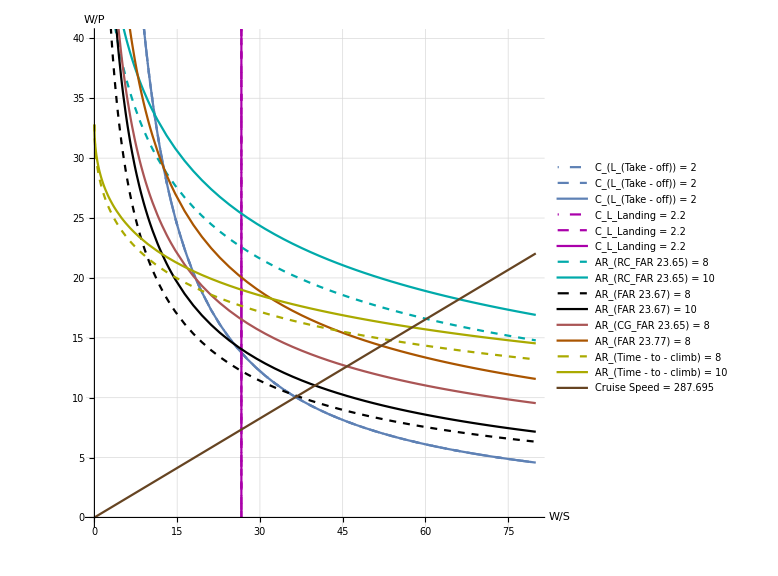

```mathematica
Show[{Tplot,Lplot,RC65plot,RC67plot,CGR65plot,CGR77plot,RCTCplot,CSplot},ImageSize->Large]
```